#### Steering distillation

```mathematica
Array[σ,4,0];
σ[0]=({{1, 0}, {0, 1}});
σ[1]=PauliMatrix[1];
σ[2]=PauliMatrix[2];
σ[3]=PauliMatrix[3];
σ4[0]={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
ArrayDepth[{σ[0],σ[1],σ[2],σ[3]}]
```

3

```mathematica
u=({{1},{0}});
d=({{0},{1}});
u1=({{1},{0},{0},{0}});
u2=({{0},{1},{0},{0}});
u3=({{0},{0},{1},{0}});
u4=({{0},{0},{0},{1}});
p=Simplify[Cos[θ]u+Sin[θ]d];
m=Simplify[Cos[θ]u-Sin[θ]d];
ut=ConjugateTranspose[u];
dt=ConjugateTranspose[d];
pt=Simplify[ConjugateTranspose[p],0<θ<π];
mt=Simplify[ConjugateTranspose[m],0<θ<π];
```

```mathematica
ψg=Simplify[Cos[θ](KroneckerProduct[u,u,u])+Sin[θ](KroneckerProduct[d,d,d])];
ψgT=Simplify[ConjugateTranspose[ψg],0<θ<π];
ρg=Simplify[ψg.ψgT];
MatrixForm[ρg]
```

(Cos[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | Cos[θ] Sin[θ]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Cos[θ] Sin[θ] | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2)

```mathematica
ψg4=Simplify[Cos[θ](KroneckerProduct[u,u,u,u])+Sin[θ](KroneckerProduct[d,d,d,d])];
ψg4T=Simplify[ConjugateTranspose[ψg4],0<θ<π];
ρg4=Simplify[ψg4.ψg4T];
MatrixForm[ρg4];
```

```mathematica
ψw=Simplify[c0(KroneckerProduct[u,u,d])+c1(KroneckerProduct[u,d,u])+c2(KroneckerProduct[d,u,u])];
ψwT=Simplify[ConjugateTranspose[ψw],{0<c1<1,0<c2<1,0<c0<1}];
ρw=Simplify[ψw.ψwT];
MatrixForm[ρw]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0 | c0 c2 | 0 | 0 | 0
0 | c0 c1 | c1^2 | 0 | c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c2 | c1 c2 | 0 | c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ψw4=Simplify[c0(KroneckerProduct[u,u,u,d])+c1(KroneckerProduct[u,u,d,u])+c2(KroneckerProduct[u,d,u,u])+c3(KroneckerProduct[d,u,u,u])];
ψw4T=Simplify[ConjugateTranspose[ψw4],{0<c0<1,0<c1<1,0<c2<1,0<c3<1}];
ρw4=Simplify[ψw4.ψw4T];
MatrixForm[ρw4]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0 | c0 c2 | 0 | 0 | 0 | c0 c3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c1 | c1^2 | 0 | c1 c2 | 0 | 0 | 0 | c1 c3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c2 | c1 c2 | 0 | c2^2 | 0 | 0 | 0 | c2 c3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c3 | c1 c3 | 0 | c2 c3 | 0 | 0 | 0 | c3^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ψ4=Simplify[k0(KroneckerProduct[u1,u1])+k1(KroneckerProduct[u2,u2])+k2(KroneckerProduct[u3,u3])+k3(KroneckerProduct[u4,u4])];
ψ4T=Simplify[ConjugateTranspose[ψ4],{0<k0<1,0<k1<1,0<k2<1,0<k3<1}];
ρ4=Simplify[ψ4.ψ4T];
MatrixForm[ρ4]
```

(k0^2 | 0 | 0 | 0 | 0 | k0 k1 | 0 | 0 | 0 | 0 | k0 k2 | 0 | 0 | 0 | 0 | k0 k3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
k0 k1 | 0 | 0 | 0 | 0 | k1^2 | 0 | 0 | 0 | 0 | k1 k2 | 0 | 0 | 0 | 0 | k1 k3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
k0 k2 | 0 | 0 | 0 | 0 | k1 k2 | 0 | 0 | 0 | 0 | k2^2 | 0 | 0 | 0 | 0 | k2 k3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
k0 k3 | 0 | 0 | 0 | 0 | k1 k3 | 0 | 0 | 0 | 0 | k2 k3 | 0 | 0 | 0 | 0 | k3^2)

```mathematica
lf0=({{1/k0, 0, 0, 0}, {0, 1/k1, 0, 0}, {0, 0, 1/k2, 0}, {0, 0, 0, 1/k3}});lf1=({{a, 0, 0, 0}, {0, b, 0, 0}, {0, 0, c, 0}, {0, 0, 0, d}});
MatrixForm[Simplify[KroneckerProduct[σ4[0],lf0].ρ4.KroneckerProduct[σ4[0],lf0]]]
```

(1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1)

#### Distillation of GGHZ state, untrusted party is Alice(1SDI) and A and B in (2SDI)

#### Assemblages in 1SDI

```mathematica
S100=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,σ[0],σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,σ[0],σ[0]]]];
s100=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].S100.KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].S100.KroneckerProduct[d,σ[0],σ[0]]];
S101=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,σ[0],σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,σ[0],σ[0]]]];
s101=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].S101.KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].S101.KroneckerProduct[d,σ[0],σ[0]]];
S110=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,σ[0],σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,σ[0],σ[0]]]];
s110=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].S110.KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].S110.KroneckerProduct[d,σ[0],σ[0]]];
S111=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,σ[0],σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,σ[0],σ[0]]]];
s111=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].S111.KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].S111.KroneckerProduct[d,σ[0],σ[0]]];
MatrixForm[(*s100+s110+*)s111(*+s111*)]
```

(Cos[θ]^2/2 | 0 | 0 | -1/2 Cos[θ] Sin[θ]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-1/2 Cos[θ] Sin[θ] | 0 | 0 | Sin[θ]^2/2)

```mathematica
g100=({{1/2, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});g101=({{1/4, 0, 0, 1/4}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1/4, 0, 0, 1/4}});g110=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1/2}});g111=({{1/4, 0, 0, -1/4}, {0, 0, 0, 0}, {0, 0, 0, 0}, {-1/4, 0, 0, 1/4}});
```

```mathematica
Assemblages in 2SDI
```

2 Assemblages in SDI

```mathematica
S20000=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]+σ[3])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]+σ[3])/2,σ[0]]]];
s20000=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S20000.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S20000.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S20000.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S20000.KroneckerProduct[d,d,σ[0]]];
S20100=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]-σ[3])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]-σ[3])/2,σ[0]]]];
s20100=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S20100.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S20100.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S20100.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S20100.KroneckerProduct[d,d,σ[0]]];
S21000=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]+σ[3])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]+σ[3])/2,σ[0]]]];
s21000=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S21000.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S21000.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S21000.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S21000.KroneckerProduct[d,d,σ[0]]];
S21100=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]-σ[3])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]-σ[3])/2,σ[0]]]];
s21100=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S21100.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S21100.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S21100.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S21100.KroneckerProduct[d,d,σ[0]]];
S20011=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]+σ[1])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]+σ[1])/2,σ[0]]]];
s20011=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S20011.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S20011.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S20011.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S20011.KroneckerProduct[d,d,σ[0]]];
S20111=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]-σ[1])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]-σ[1])/2,σ[0]]]];
s20111=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S20111.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S20111.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S20111.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S20111.KroneckerProduct[d,d,σ[0]]];
S21011=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]+σ[1])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]+σ[1])/2,σ[0]]]];
s21011=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S21011.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S21011.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S21011.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S21011.KroneckerProduct[d,d,σ[0]]];
S21111=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]-σ[1])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]-σ[1])/2,σ[0]]]];
s21111=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S21111.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S21111.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S21111.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S21111.KroneckerProduct[d,d,σ[0]]];
MatrixForm[s20000]
MatrixForm[s20100]
MatrixForm[s21000]
MatrixForm[s21100]
MatrixForm[s20011]
MatrixForm[s20111]
MatrixForm[s21011]
MatrixForm[s21111]
```

(Cos[θ]^2 | 0
0 | 0)

(0 | 0
0 | 0)

(0 | 0
0 | 0)

(0 | 0
0 | Sin[θ]^2)

(Cos[θ]^2/4 | 1/4 Cos[θ] Sin[θ]
1/4 Cos[θ] Sin[θ] | Sin[θ]^2/4)

(Cos[θ]^2/4 | -1/4 Cos[θ] Sin[θ]
-1/4 Cos[θ] Sin[θ] | Sin[θ]^2/4)

(Cos[θ]^2/4 | -1/4 Cos[θ] Sin[θ]
-1/4 Cos[θ] Sin[θ] | Sin[θ]^2/4)

(Cos[θ]^2/4 | 1/4 Cos[θ] Sin[θ]
1/4 Cos[θ] Sin[θ] | Sin[θ]^2/4)

```mathematica
S20001=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]+σ[1])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]+σ[1])/2,σ[0]]]];
s20001=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S20001.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S20001.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S20001.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S20001.KroneckerProduct[d,d,σ[0]]];
S20101=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]-σ[1])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]-σ[1])/2,σ[0]]]];
s20101=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S20101.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S20101.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S20101.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S20101.KroneckerProduct[d,d,σ[0]]];
S21001=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]+σ[1])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]+σ[1])/2,σ[0]]]];
s21001=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S21001.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S21001.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S21001.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S21001.KroneckerProduct[d,d,σ[0]]];
S21101=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]-σ[1])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]-σ[1])/2,σ[0]]]];
s21101=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S21101.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S21101.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S21101.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S21101.KroneckerProduct[d,d,σ[0]]];
S20010=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]+σ[3])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]+σ[3])/2,σ[0]]]];
s20010=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S20010.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S20010.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S20010.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S20010.KroneckerProduct[d,d,σ[0]]];
S20110=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]-σ[3])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]-σ[3])/2,σ[0]]]];
s20110=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S20110.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S20110.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S20110.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S20110.KroneckerProduct[d,d,σ[0]]];
S21010=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]+σ[3])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]+σ[3])/2,σ[0]]]];
s21010=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S21010.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S21010.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S21010.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S21010.KroneckerProduct[d,d,σ[0]]];
S21110=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]-σ[3])/2,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]-σ[3])/2,σ[0]]]];
s21110=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].S21110.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].S21110.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].S21110.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].S21110.KroneckerProduct[d,d,σ[0]]];
MatrixForm[s20001]
MatrixForm[s20101]
MatrixForm[s21001]
MatrixForm[s21101]
MatrixForm[s20010]
MatrixForm[s20110]
MatrixForm[s21010]
MatrixForm[s21110]
```

(Cos[θ]^2/2 | 0
0 | 0)

(Cos[θ]^2/2 | 0
0 | 0)

(0 | 0
0 | Sin[θ]^2/2)

(0 | 0
0 | Sin[θ]^2/2)

(Cos[θ]^2/2 | 0
0 | 0)

(0 | 0
0 | Sin[θ]^2/2)

(Cos[θ]^2/2 | 0
0 | 0)

(0 | 0
0 | Sin[θ]^2/2)

```mathematica
g20000=({{1/2, 0}, {0, 0}});g20100=({{0, 0}, {0, 0}});g21000=({{0, 0}, {0, 0}});
g21100=({{0, 0}, {0, 1/2}});g20011=({{1/4, 1/4}, {1/4, 1/4}});g20111=({{1/4, -1/4}, {-1/4, 1/4}});g21011=({{1/4, -1/4}, {-1/4, 1/4}});g21111=({{1/4, 1/4}, {1/4, 1/4}});
```

```mathematica
g20001=({{1/2, 0}, {0, 0}});g20101=({{1/2, 0}, {0, 0}});g21001=({{0, 0}, {0, 1/2}});
g21101=({{0, 0}, {0, 1/2}});g20010=({{1/2, 0}, {0, 0}});g20110=({{0, 0}, {0, 1/2}});g21010=({{1/2, 0}, {0, 0}});
g21110=({{0, 0}, {0, 1/2}});
```

#### Local filtering operation by Bob and Charlie in 1SDI scenario

```mathematica
Strategy 1 (one party contribution)
```

contribution one party Strategy

```mathematica
K0=Simplify[Tan[θ](u.ut)+d.dt];
MatrixForm[K0]
K0T=Simplify[ConjugateTranspose[K0],{0<θ<π,0<Tan[θ]<1}];
MatrixForm[K0T]
K1=Simplify[√(1-Tan[θ]^2)(u.ut)];
MatrixForm[K1]
K1T=Simplify[ConjugateTranspose[K1],{0<θ<π,0<Tan[θ]<1}];
MatrixForm[K1T]
Simplify[K0T.K0+K1T.K1]
```

(Tan[θ] | 0
0 | 1)

(Tan[θ] | 0
0 | 1)

(√(1-Tan[θ]^2) | 0
0 | 0)

(√(1-Tan[θ]^2) | 0
0 | 0)

{{1,0},{0,1}}

```mathematica
Strategy 2 (Equal contribution)
```

2 contribution Equal Strategy

```mathematica
E0=Simplify[√Tan[θ](u.ut)+d.dt];
MatrixForm[E0]
E0T=Simplify[ConjugateTranspose[E0],{0<θ<π,0<Tan[θ]<1}];
MatrixForm[E0T]
E1=Simplify[√(1-Tan[θ])(u.ut)];
MatrixForm[E1]
E1T=Simplify[ConjugateTranspose[E1],{0<θ<π,0<Tan[θ]<1}];
MatrixForm[E1T]
Simplify[E0T.E0+E1T.E1]
```

(√Tan[θ] | 0
0 | 1)

(√Tan[θ] | 0
0 | 1)

(√(1-Tan[θ]) | 0
0 | 0)

(√(1-Tan[θ]) | 0
0 | 0)

{{1,0},{0,1}}

```mathematica
Strategy 3 (Unequal contribution)
```

3 contribution Strategy Unequal

```mathematica
F0=Simplify[(Tan[θ])^(1/n)(u.ut)+d.dt];
MatrixForm[F0]
F0T=Simplify[ConjugateTranspose[F0],{0<θ<π,0<Tan[θ]<1,0<n<500}];
MatrixForm[F0T]
F1=Simplify[√(1-(Tan[θ])^(2/n))(u.ut)];
MatrixForm[F1]
F1T=Simplify[ConjugateTranspose[F1],{(*0<θ<π,*)(*0<Tan[θ]<1,*)0<Tan[θ]^(2/n)<1}];
MatrixForm[F1T]
Simplify[F0T.F0+F1T.F1]
F2=Simplify[(Tan[θ])^((n-1)/n)(u.ut)+d.dt];
MatrixForm[F2]
F2T=Simplify[ConjugateTranspose[F2],{0<θ<π,0<Tan[θ]<1,0<n<500}];
MatrixForm[F2T]
F3=Simplify[√(1-(Tan[θ])^(2(n-1)/n))(u.ut)];
MatrixForm[F3]
F3T=Simplify[ConjugateTranspose[F3],{(*0<θ<π,*)(*0<Tan[θ]<1,*)0<Tan[θ]^(2/n)<1}];
MatrixForm[F3T]
Simplify[F2T.F2+F3T.F3]
```

(Tan[θ]^(1/n) | 0
0 | 1)

(Tan[θ]^(1/n) | 0
0 | 1)

(√(1-Tan[θ]^(2/n)) | 0
0 | 0)

(Conjugate[√(1-Tan[θ]^(2/n))] | 0
0 | 0)

{{Tan[θ]^(2/n)+Conjugate[√(1-Tan[θ]^(2/n))] √(1-Tan[θ]^(2/n)),0},{0,1}}

(Tan[θ]^((-1+n)/n) | 0
0 | 1)

(Tan[θ]^((-1+n)/n) | 0
0 | 1)

(√(1-Tan[θ]^(2-2/n)) | 0
0 | 0)

(Conjugate[√(1-Tan[θ]^(2-2/n))] | 0
0 | 0)

{{Tan[θ]^(2-2/n)+Conjugate[√(1-Tan[θ]^(2-2/n))] √(1-Tan[θ]^(2-2/n)),0},{0,1}}

```mathematica
Success probability 1SDI
```

probability SDI Success

```mathematica
P11SGHZ=Simplify[Tr[KroneckerProduct[K0,σ[0]].(s101+s111).KroneckerProduct[K0T,σ[0]]]]
```

2 Sin[θ]^2

```mathematica
P21SGHZ=Simplify[Tr[KroneckerProduct[E0,E0].(s100+s110).KroneckerProduct[E0T,E0T]]]
```

2 Sin[θ]^2

```mathematica
P31SGHZ=Simplify[Tr[KroneckerProduct[F0,F2].(s101+s111).KroneckerProduct[F0T,F2T]](*+Tr[KroneckerProduct[F0,F2].(s101+s111).KroneckerProduct[F0T,F2T]]*)]
```

2 Sin[θ]^2

```mathematica
Success probability 2SDI
```

2 probability SDI Success

```mathematica
P12SGHZ=Simplify[Tr[K0.(s20000+s20100+s21000+s21100).K0T]]
P22SGHZ=Simplify[Tr[K0.(s20001+s20101+s21001+s21101).K0T]]
P32SGHZ=Simplify[Tr[K0.(s20010+s20110+s21010+s21110).K0T]]
P42SGHZ=Simplify[Tr[K0.(s20011+s20111+s21011+s21111).K0T]]
```

2 Sin[θ]^2

2 Sin[θ]^2

2 Sin[θ]^2

«1 more identical outputs»

```mathematica
Failure probability
```

Failure probability

```mathematica
Pf11SGHZ=Simplify[Tr[KroneckerProduct[K1,σ[0]].(s101+s111).KroneckerProduct[K1T,σ[0]]]]
```

Cos[2 θ]

```mathematica
Pf21SGHZ=Simplify[Tr[KroneckerProduct[E1,E1].(s100+s110).KroneckerProduct[E1,E1]]+Tr[KroneckerProduct[E0,E1].(s100+s110).KroneckerProduct[E0,E1]]+Tr[KroneckerProduct[E1,E0].(s100+s110).KroneckerProduct[E1,E0]]]
```

Cos[2 θ]

```mathematica
Pf31SGHZ=Simplify[Tr[KroneckerProduct[F0,F1].(s101+s111).KroneckerProduct[F0,F1]]+Tr[KroneckerProduct[F0,F3].(s101+s111).KroneckerProduct[F0,F3]]+Tr[KroneckerProduct[F1,F0].(s101+s111).KroneckerProduct[F1,F0]]+
Tr[KroneckerProduct[F1,F2].(s101+s111).KroneckerProduct[F1,F2]]+Tr[KroneckerProduct[F1,F3].(s101+s111).KroneckerProduct[F1,F3]]+Tr[KroneckerProduct[F2,F1].(s101+s111).KroneckerProduct[F2,F1]]+Tr[KroneckerProduct[F2,F3].(s101+s111).KroneckerProduct[F2,F3]]+Tr[KroneckerProduct[F3,F0].(s101+s111).KroneckerProduct[F3,F0]]+Tr[KroneckerProduct[F3,F1].(s101+s111).KroneckerProduct[F3,F1]]+Tr[KroneckerProduct[F3,F2].(s101+s111).KroneckerProduct[F3,F2]]+
Tr[KroneckerProduct[F0,F0].(s101+s111).KroneckerProduct[F0,F0]]+Tr[KroneckerProduct[F3,F3].(s101+s111).KroneckerProduct[F3,F3]]+Tr[KroneckerProduct[F1,F1].(s101+s111).KroneckerProduct[F1,F1]]+Tr[KroneckerProduct[F2,F2].(s101+s111).KroneckerProduct[F2,F2]]]
```

4 Cos[θ]^2

```mathematica
Simplify[P11SGHZ+Pf11SGHZ]
```

1

```mathematica
Simplify[P21SGHZ+Pf21SGHZ]
```

1

```mathematica
Simplify[P31SGHZ+Pf31SGHZ]
```

4

#### Assemblage fidelity for finite copy 1SDI

```mathematica
u00=({{1},{0},{0},{0}});
u01=({{0},{1},{0},{0}});
u10=({{0},{0},{1},{0}});
u11=({{0},{0},{0},{1}});
ut00=ConjugateTranspose[u00];
ut01=ConjugateTranspose[u01];
ut10=ConjugateTranspose[u10];
ut11=ConjugateTranspose[u11];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD100=Simplify[Pgs*g100+Pgf*s100];
gD101=Simplify[Pgs*g101+Pgf*s101];
gD110=Simplify[Pgs*g110+Pgf*s110];
gD111=Simplify[Pgs*g111+Pgf*s111];
```

```mathematica
Fg0=Simplify[1/(√2)(√((ut00.gD100.u00))+√(ut11.gD110.u11))]
```

{{1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))}}

```mathematica
Simplify[√Tr[g100.gD100]+√Tr[g110.gD110]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg1=Simplify[1/(√4)(√((ut00.gD101.u00)+(ut00.gD101.u11)+(ut11.gD101.u00)+(ut11.gD101.u11))+√((ut00.gD111.u00)-(ut00.gD111.u11)-(ut11.gD111.u00)+(ut11.gD111.u11)))]
```

{{1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))}}

```mathematica
Simplify[√Tr[g101.gD101]+√Tr[g111.gD111]]
```

1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))

```mathematica
θ=1.5;cp=356;
Simplify[Fg0]//N
(*Simplify[Fg1]//N*)
Clear[θ,cp]
```

{{0.999903}}

{{1.00602}}

```mathematica
GHZ 1SDI
```

```mathematica
{{θ, cp=2, 5, 10, 50, 100, 380, □, □, □}, {0.1, 0.779308, 0.793939, 0.81593, 0.922288, 0.972324, 0.999903, □, □, □}, {0.2, cp=2, 5, 10, 50, 91, □, □, □, □}, {0.2, 0.847826, 0.88335, 0.924311, 0.997281, 0.999907, □, □, □, □}, {0.3, □, □, □, 20, 38, □, □, □, □}, {0.3, 0.905727, 0.948154, 0.980469, 0.99716, 0.99991, □, □, □, □}, {0.4, □, □, □, 20, □, □, □, □, □}, {0.4, 0.949495, 0.98321, 0.997263, 0.999926, □, □, □, □, □}, {0.5, □, □, 10, 11, □, □, □, □, □}, {0.5, 0.978352, 0.996617, 0.999844, 0.999916, □, □, □, □, □}, {0.6, □, □, 7, □, □, □, □, □, □}, {0.6, 0.993824, 0.999707, 0.999962, □, □, □, □, □, □}, {0.7, □, 4, □, □, □, □, □, □, □}, {0.7, 0.999382, 0.999982, □, □, □, □, □, □, □}, {0.8, □, □, □, □, □, □, □, □, □}, {0.8, 1, □, □, □, □, □, □, □, □}, {0.9, □, □, □, □, □, □, □, □, □}, {0.9, 0.999667, 4/0.99998, 1, □, □, □, □, □, □}}
{{1, 0.9962, 0.99932, 7/0.9998, □, □, □, □, □, □}, {1.1, 0.9844, 0.9942, 8/0.9999, □, □, □, □, □, □}, {1.2, 0.959, 0.975717, 12/0.9999, □, □, □, □, □, □}, {1.3, 0.9162, 0.932413, 0.994223, 24/0.9999, □, □, □, □, □}}
{{1.4, 0.854477, 0.85903, 0.957649, 60/0.9999, □, □, □, □, □}, {1.5, 0.774137, 0.766482, 0.84465, 0.947733, 0.982525, 356/0.9999, □, □, □}, {0.9, □, □, □, □, □, □, □, □, □}, {0.9, 0.999667, □, □, □, □, □, □, □, □}}
```

```mathematica
GHZ 2SDI
```

```mathematica
θ=1.5;cp=356;
Simplify[Fg0]//N
(*Simplify[Fg1]//N*)
Clear[θ,cp]
```

{{0.999903}}

```mathematica
{{θ, cp=2, 5, 10, 50, 100, 178, □, □, □}, {0.1, 0.799429, 0.844704, 0.887622, 0.98256, 0.997759, 0.999904, □, □, □}, {0.2, cp=2, 5, 10, 44, □, □, □, □, □}, {0.2, 0.87448, 0.935071, 0.974238, 0.99991, □, □, □, □, □}, {0.3, □, □, □, 19, □, □, □, □, □}, {0.3, 0.930623, 0.980756, 0.997293, 0.99991, □, □, □, □, □}, {0.4, □, □, 10, □, □, □, □, □, □}, {0.4, 0.968063, 0.996603, 0.9999, □, □, □, □, □, □}, {0.5, □, □, 6, □, □, □, □, □, □}, {0.5, 0.98905, 0.999735, 0.99992, □, □, □, □, □, □}, {0.6, □, □, □, □, □, □, □, □, □}, {0.6, 0.997833, 1, □, □, □, □, □, □, □}, {0.7, □, 3, □, □, □, □, □, □, □}, {0.7, 0.999896, 0.999992, □, □, □, □, □, □, □}, {0.8, □, □, □, □, □, □, □, □, □}, {0.8, 1, □, □, □, □, □, □, □, □}, {0.9, □, □, □, □, □, □, □, □, □}, {0.9, 0.999667, 3/0.99998, 1, □, □, □, □, □, □}}
{{1, 0.9962, 5/0.99998, □, □, □, □, □, □, □}, {1.1, 0.9844, 0.999376, 7/0.9999, □, □, □, □, □, □}, {1.2, 0.959, 0.993968, 12/0.9999, □, □, □, □, □, □}, {1.3, 0.9162, 0.971311, 0.994223, 24/0.9999, □, □, □, □, □}}
{{1.4, 0.854477, 0.913705, 0.957649, 60/0.9999, □, □, □, □, □}, {1.5, 0.774137, 0.809114, 0.84465, 0.947733, 0.982525, 356/0.9999, □, □, □}, {0.9, □, □, □, □, □, □, □, □, □}, {0.9, 0.999667, □, □, □, □, □, □, □, □}}
```

#### Assemblage fidelity for finite copy 2SDI

```mathematica
u00=({{1},{0},{0},{0}});
u01=({{0},{1},{0},{0}});
u10=({{0},{0},{1},{0}});
u11=({{0},{0},{0},{1}});
ut00=ConjugateTranspose[u00];
ut01=ConjugateTranspose[u01];
ut10=ConjugateTranspose[u10];
ut11=ConjugateTranspose[u11];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD20000=Simplify[Pgs*g20000+Pgf*s20000];
gD20100=Simplify[Pgs*g20100+Pgf*s20100];
gD21000=Simplify[Pgs*g21000+Pgf*s21000];
gD21100=Simplify[Pgs*g21100+Pgf*s21100];
gD20011=Simplify[Pgs*g20011+Pgf*s20011];
gD20111=Simplify[Pgs*g20111+Pgf*s20111];
gD21011=Simplify[Pgs*g21011+Pgf*s21011];
gD21111=Simplify[Pgs*g21111+Pgf*s21111];
gD20001=Simplify[Pgs*g20001+Pgf*s20001];
gD20101=Simplify[Pgs*g20101+Pgf*s20101];
gD21001=Simplify[Pgs*g21001+Pgf*s21001];
gD21101=Simplify[Pgs*g21101+Pgf*s21101];
gD20010=Simplify[Pgs*g20010+Pgf*s20010];
gD20110=Simplify[Pgs*g20110+Pgf*s20110];
gD21010=Simplify[Pgs*g21010+Pgf*s21010];
gD21110=Simplify[Pgs*g21110+Pgf*s21110];
```

```mathematica
Fg200=Simplify[√Tr[g20000.gD20000]+√Tr[g20100.gD20100]+√Tr[g21000.gD21000]+√Tr[g21100.gD21100]]
Fg201=Simplify[√Tr[g20001.gD20001]+√Tr[g20101.gD20101]+√Tr[g21001.gD21001]+√Tr[g21101.gD21101]]
Fg210=Simplify[√Tr[g20010.gD20010]+√Tr[g20110.gD20110]+√Tr[g21010.gD21010]+√Tr[g21110.gD21110]]
Fg211=Simplify[√Tr[g20011.gD20011]+√Tr[g20111.gD20111]+√Tr[g21011.gD21011]+√Tr[g21111.gD21111]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

√(1-Cos[θ]^2 Cos[2 θ]^(-1+cp))+(√(2-Cos[2 θ]^(-1+cp)+Cos[2 θ]^cp))/(√2)

√(1-Cos[θ]^2 Cos[2 θ]^(-1+cp))+(√(2-Cos[2 θ]^(-1+cp)+Cos[2 θ]^cp))/(√2)

(√(8+2 Cos[2 θ]^(-1+cp) (-3+Sin[2 θ])))/(√2)

```mathematica
θ=π/2;cp=2;
Simplify[Fg200]//N
Simplify[Fg201]//N
Simplify[Fg210]
Simplify[Fg211]
Clear[θ,cp]
```

0.707107

2.41421

1+√2

√7

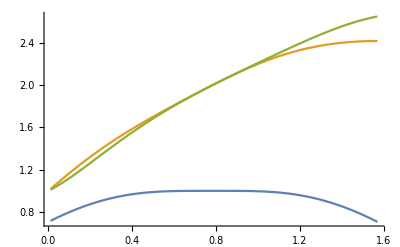

```mathematica
cp=2;
Plot[{1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp)),(*√(1-Cos[θ]^2 Cos[2 θ]^(-1+cp))+(√(2-Cos[2 θ]^(-1+cp)+Cos[2 θ]^cp))/(√2),*)√(1-Cos[θ]^2 Cos[2 θ]^(-1+cp))+(√(2-Cos[2 θ]^(-1+cp)+Cos[2 θ]^cp))/(√2),(√(8+2 Cos[2 θ]^(-1+cp) (-3+Sin[2 θ])))/(√2)},{θ,0.01,π/2}]
Clear[cp]
```

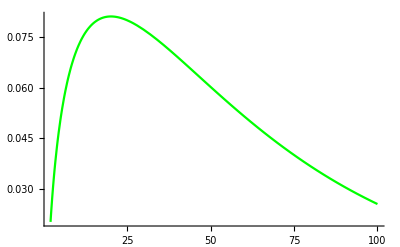

```mathematica
θ=0.1;
Plot[{-1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))+1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))},{cp,2,100}(*,{cp,2,5}*),PlotStyle->{Blue,Green}]
Clear[θ]
```

```mathematica
cp=100;θ=0.1
Simplify[{1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))-1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))}]
Clear[cp,θ]
```

0.1

{-0.0254351}

```mathematica
4-partite GHZ state
```

#### Assemblages in 1SDI

```mathematica
S1000=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,σ[0],σ[0],σ[0]].ρg4.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,σ[0],σ[0],σ[0]]]];
s1000=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0],σ[0]]].S1000.KroneckerProduct[u,σ[0],σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0],σ[0]]].S1000.KroneckerProduct[d,σ[0],σ[0],σ[0]]];
S2000=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,σ[0],σ[0],σ[0]].ρg4.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,σ[0],σ[0],σ[0]]]];
s2000=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0],σ[0]]].S2000.KroneckerProduct[u,σ[0],σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0],σ[0]]].S2000.KroneckerProduct[d,σ[0],σ[0],σ[0]]];
S3000=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,σ[0],σ[0],σ[0]].ρg4.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,σ[0],σ[0],σ[0]]]];
s3000=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0],σ[0]]].S3000.KroneckerProduct[u,σ[0],σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0],σ[0]]].S3000.KroneckerProduct[d,σ[0],σ[0],σ[0]]];
S4000=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,σ[0],σ[0],σ[0]].ρg4.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,σ[0],σ[0],σ[0]]]];
s4000=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0],σ[0]]].S4000.KroneckerProduct[u,σ[0],σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0],σ[0]]].S4000.KroneckerProduct[d,σ[0],σ[0],σ[0]]];
MatrixForm[(*s100+s110+*)s4000(*+s111*)]
```

(Cos[θ]^2/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 Cos[θ] Sin[θ]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 Cos[θ] Sin[θ] | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2/2)

```mathematica
g1000=({{1/2, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});g2000=({{1/4, 0, 0, 0, 0, 0, 0, 1/4}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {1/4, 0, 0, 0, 0, 0, 0, 1/4}});g3000=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1/2}});g4000=({{1/4, 0, 0, 0, 0, 0, 0, -1/4}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {-1/4, 0, 0, 0, 0, 0, 0, 1/4}});
```

```mathematica
P41SGHZ=Simplify[Tr[KroneckerProduct[K0,σ[0],σ[0]].(s2000+s4000).KroneckerProduct[K0T,σ[0],σ[0]]]]
```

2 Sin[θ]^2

```mathematica
Simplify[Tr[KroneckerProduct[K0,σ[0],σ[0],σ[0]].(ρg4).KroneckerProduct[K0T,σ[0],σ[0],σ[0]]]]
```

2 Sin[θ]^2

```mathematica
L0=({{Tan[θ]^(1/q), 0}, {0, 1}});L1=({{Tan[θ]^(1/r), 0}, {0, 1}});L2=({{Tan[θ]^(1-1/q-1/r), 0}, {0, 1}});
```

```mathematica
MatrixForm[Simplify[KroneckerProduct[L0,L1,L2,σ[0]].(ρg4).KroneckerProduct[L0,L1,L2,σ[0]]]]
```

(Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[θ]^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Sin[θ]^2)

```mathematica
1-sided DI for GGHZ state (n = 4)
```

```mathematica
For[l=0,l<2,l++,
For[i=0,i<2,i++,
S[i+1+l(2),0,0,0]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[1+l(2)])/2,σ[0],σ[0],σ[0]].ρg4.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[1+l(2)])/2,σ[0],σ[0],σ[0]]]];
s[i+1+l(2),0,0,0]=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0],σ[0]]].S[i+1+l(2),0,0,0].KroneckerProduct[u,σ[0],σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0],σ[0]]].S[i+1+l(2),0,0,0].KroneckerProduct[d,σ[0],σ[0],σ[0]]];
θ=π/4;
g[i+1+l(2),0,0,0]=s[i+1+l(2),0,0,0];
Clear[θ];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD[i+1+l(2),0,0,0]=Simplify[Pgs*g[i+1+l(2),0,0,0]+Pgf*s[i+1+l(2),0,0,0]];]];
Clear[l,q,r,i,j,k]
```

```mathematica
MatrixForm[g[4,0,0,0]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2)

```mathematica
Assemblage fideity
```

```mathematica
Fg11=Simplify[√Tr[g[3,0,0,0].gD[3,0,0,0]]+√Tr[g[4,0,0,0].gD[4,0,0,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg12=Simplify[√Tr[g[1,0,0,0].gD[1,0,0,0]]+√Tr[g[2,0,0,0].gD[2,0,0,0]]]
```

1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))

```mathematica
2-sided DI for GGHZ state (n = 4)
```

```mathematica
For[l=0,l<2,l++,
For[q=0,q<2,q++,
(*For[r=0,r<2,r++,
*)For[i=0,i<2,i++,
For[j=0,j<2,j++,
(*For[k=0,k<2,k++,*)
(*For[l=0;l<2;l++,*)
S[i+1+l(2),j+1+q(2),0,0]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[1+l(2)])/2,(σ[0]+(-1)^j σ[1+q(2)])/2,σ[0],σ[0]].ρg4.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[1+l(2)])/2,(σ[0]+(-1)^j σ[1+q(2)])/2,σ[0],σ[0]]]];
s[i+1+l(2),j+1+q(2),0,0]=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0],σ[0]]].S[i+1+l(2),j+1+q(2),0,0].KroneckerProduct[u,u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0],σ[0]]].S[i+1+l(2),j+1+q(2),0,0].KroneckerProduct[u,d,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0],σ[0]]].S[i+1+l(2),j+1+q(2),0,0].KroneckerProduct[d,u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0],σ[0]]].S[i+1+l(2),j+1+q(2),0,0].KroneckerProduct[d,d,σ[0],σ[0]]];
θ=π/4;
g[i+1+l(2),j+1+q(2),0,0]=s[i+1+l(2),j+1+q(2),0,0];
Clear[θ];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD[i+1+l(2),j+1+q(2),0,0]=Simplify[Pgs*g[i+1+l(2),j+1+q(2),0,0]+Pgf*s[i+1+l(2),j+1+q(2),0,0]];]]]];
Clear[l,q,r,i,j,k]
```

```mathematica
MatrixForm[gD[1,1,0,0]]
```

(1/8 (1+Cos[2 θ]^cp) | 0 | 0 | 1/8 (1+Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/8 (1+Cos[2 θ]^(-1+cp) (-1+Sin[2 θ])) | 0 | 0 | 1/8 (1-Cos[2 θ]^cp))

```mathematica
Assemblage fideity
```

```mathematica
Fg211=Simplify[√Tr[g[3,3,0,0].gD[3,3,0,0]]+√Tr[g[3,4,0,0].gD[3,4,0,0]]+√Tr[g[4,3,0,0].gD[4,3,0,0]]+√Tr[g[4,4,0,0].gD[4,4,0,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg210=Simplify[√Tr[g[3,1,0,0].gD[3,1,0,0]]+√Tr[g[3,2,0,0].gD[3,2,0,0]]+√Tr[g[4,1,0,0].gD[4,1,0,0]]+√Tr[g[4,2,0,0].gD[4,2,0,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg201=Simplify[√Tr[g[1,3,0,0].gD[1,3,0,0]]+√Tr[g[1,4,0,0].gD[1,4,0,0]]+√Tr[g[2,3,0,0].gD[2,3,0,0]]+√Tr[g[2,4,0,0].gD[2,4,0,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg200=Simplify[√Tr[g[1,1,0,0].gD[1,1,0,0]]+√Tr[g[1,2,0,0].gD[1,2,0,0]]+√Tr[g[2,1,0,0].gD[2,1,0,0]]+√Tr[g[2,2,0,0].gD[2,2,0,0]]]
```

1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))

```mathematica
3-sided DI for GGHZ state (n = 4)
```

```mathematica
For[l=0,l<2,l++,
For[q=0,q<2,q++,
For[r=0,r<2,r++,
For[i=0,i<2,i++,
For[j=0,j<2,j++,
For[k=0,k<2,k++,
(*For[l=0;l<2;l++,*)
S[i+1+l(2),j+1+q(2),k+1+r(2),0]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[1+l(2)])/2,(σ[0]+(-1)^j σ[1+q(2)])/2,(σ[0]+(-1)^k σ[1+r(2)])/2,σ[0]].ρg4.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[1+l(2)])/2,(σ[0]+(-1)^j σ[1+q(2)])/2,(σ[0]+(-1)^k σ[1+r(2)])/2,σ[0]]]];
s[i+1+l(2),j+1+q(2),k+1+r(2),0]=Simplify[ConjugateTranspose[KroneckerProduct[u,u,u,σ[0]]].S[i+1+l(2),j+1+q(2),k+1+r(2),0].KroneckerProduct[u,u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,u,d,σ[0]]].S[i+1+l(2),j+1+q(2),k+1+r(2),0].KroneckerProduct[u,u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,u,σ[0]]].S[i+1+l(2),j+1+q(2),k+1+r(2),0].KroneckerProduct[u,d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,d,σ[0]]].S[i+1+l(2),j+1+q(2),k+1+r(2),0].KroneckerProduct[u,d,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,u,σ[0]]].S[i+1+l(2),j+1+q(2),k+1+r(2),0].KroneckerProduct[d,u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,d,σ[0]]].S[i+1+l(2),j+1+q(2),k+1+r(2),0].KroneckerProduct[d,u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,u,σ[0]]].S[i+1+l(2),j+1+q(2),k+1+r(2),0].KroneckerProduct[d,d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,d,σ[0]]].S[i+1+l(2),j+1+q(2),k+1+r(2),0].KroneckerProduct[d,d,d,σ[0]]];
θ=π/4;
g[i+1+l(2),j+1+q(2),k+1+r(2),0]=s[i+1+l(2),j+1+q(2),k+1+r(2),0];
Clear[θ];
Pgf=Simplify[(1-(2 Sin[θ]^2))^(cp-1)];Pgs=Simplify[1-(1-(2 Sin[θ]^2))^(cp-1)];
gD[i+1+l(2),j+1+q(2),k+1+r(2),0]=Simplify[Pgs*g[i+1+l(2),j+1+q(2),k+1+r(2),0]+Pgf*s[i+1+l(2),j+1+q(2),k+1+r(2),0]];]]]]]];
Clear[l,q,r,i,j,k]
```

```mathematica
MatrixForm[gD[2,1,1,0]]
```

(1/16 (1+Cos[2 θ]^cp) | 1/16 (-1+Cos[2 θ]^(-1+cp) (1-2 Cos[θ] Sin[θ]))
1/16 (-1+Cos[2 θ]^(-1+cp) (1-2 Cos[θ] Sin[θ])) | 1/16 (1-Cos[2 θ]^cp))

```mathematica
Assemblage fideity
```

```mathematica
For[l=0,l<2,l++,
For[q=0,q<2,q++,
For[r=0,r<2,r++,
Fg[l,q,r]:=Sum[√Tr[g[i+1+l(2),j+1+q(2),k+1+r(2),0].gD[i+1+l(2),j+1+q(2),k+1+r(2),0]],{i,0,1,1},{j,0,1,1},{k,0,1,1}]]]]
```

```mathematica
Fg[0,0,0]
```

√Tr[g[5,5,5,0].gD[5,5,5,0]]+√Tr[g[5,5,6,0].gD[5,5,6,0]]+√Tr[g[5,6,5,0].gD[5,6,5,0]]+√Tr[g[5,6,6,0].gD[5,6,6,0]]+√Tr[g[6,5,5,0].gD[6,5,5,0]]+√Tr[g[6,5,6,0].gD[6,5,6,0]]+√Tr[g[6,6,5,0].gD[6,6,5,0]]+√Tr[g[6,6,6,0].gD[6,6,6,0]]

```mathematica
Fg3111=Simplify[√Tr[g[3,3,3,0].gD[3,3,3,0]]+√Tr[g[3,3,4,0].gD[3,3,4,0]]+√Tr[g[3,4,3,0].gD[3,4,3,0]]+√Tr[g[3,4,4,0].gD[3,4,4,0]]+√Tr[g[4,3,3,0].gD[4,3,3,0]]+√Tr[g[4,3,4,0].gD[4,3,4,0]]+√Tr[g[4,4,3,0].gD[4,4,3,0]]+√Tr[g[4,4,4,0].gD[4,4,4,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg3110=Simplify[√Tr[g[3,3,1,0].gD[3,3,1,0]]+√Tr[g[3,3,2,0].gD[3,3,2,0]]+√Tr[g[3,4,1,0].gD[3,4,1,0]]+√Tr[g[3,4,2,0].gD[3,4,2,0]]+√Tr[g[4,3,1,0].gD[4,3,1,0]]+√Tr[g[4,3,2,0].gD[4,3,2,0]]+√Tr[g[4,4,1,0].gD[4,4,1,0]]+√Tr[g[4,4,2,0].gD[4,4,2,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg3101=Simplify[√Tr[g[3,1,3,0].gD[3,1,3,0]]+√Tr[g[3,1,4,0].gD[3,1,4,0]]+√Tr[g[3,2,3,0].gD[3,2,3,0]]+√Tr[g[3,2,4,0].gD[3,2,4,0]]+√Tr[g[4,1,3,0].gD[4,1,3,0]]+√Tr[g[4,1,4,0].gD[4,1,4,0]]+√Tr[g[4,2,3,0].gD[4,2,3,0]]+√Tr[g[4,2,4,0].gD[4,2,4,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg3011=Simplify[√Tr[g[1,3,3,0].gD[1,3,3,0]]+√Tr[g[1,3,4,0].gD[1,3,4,0]]+√Tr[g[1,4,3,0].gD[1,4,3,0]]+√Tr[g[1,4,4,0].gD[1,4,4,0]]+√Tr[g[2,3,3,0].gD[2,3,3,0]]+√Tr[g[2,3,4,0].gD[2,3,4,0]]+√Tr[g[2,4,3,0].gD[2,4,3,0]]+√Tr[g[2,4,4,0].gD[2,4,4,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg3100=Simplify[√Tr[g[3,1,1,0].gD[3,1,1,0]]+√Tr[g[3,1,2,0].gD[3,1,2,0]]+√Tr[g[3,2,1,0].gD[3,2,1,0]]+√Tr[g[3,2,2,0].gD[3,2,2,0]]+√Tr[g[4,1,1,0].gD[4,1,1,0]]+√Tr[g[4,1,2,0].gD[4,1,2,0]]+√Tr[g[4,2,1,0].gD[4,2,1,0]]+√Tr[g[4,2,2,0].gD[4,2,2,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg3010=Simplify[√Tr[g[1,3,1,0].gD[1,3,1,0]]+√Tr[g[1,3,2,0].gD[1,3,2,0]]+√Tr[g[1,4,1,0].gD[1,4,1,0]]+√Tr[g[1,4,2,0].gD[1,4,2,0]]+√Tr[g[2,3,1,0].gD[2,3,1,0]]+√Tr[g[2,3,2,0].gD[2,3,2,0]]+√Tr[g[2,4,1,0].gD[2,4,1,0]]+√Tr[g[2,4,2,0].gD[2,4,2,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg3001=Simplify[√Tr[g[1,1,3,0].gD[1,1,3,0]]+√Tr[g[1,1,4,0].gD[1,1,4,0]]+√Tr[g[1,2,3,0].gD[1,2,3,0]]+√Tr[g[1,2,4,0].gD[1,2,4,0]]+√Tr[g[2,1,3,0].gD[2,1,3,0]]+√Tr[g[2,1,4,0].gD[2,1,4,0]]+√Tr[g[2,2,3,0].gD[2,2,3,0]]+√Tr[g[2,2,4,0].gD[2,2,4,0]]]
```

1/2 (√(1-Cos[2 θ]^cp)+√(1+Cos[2 θ]^cp))

```mathematica
Fg3000=Simplify[√Tr[g[1,1,1,0].gD[1,1,1,0]]+√Tr[g[1,1,2,0].gD[1,1,2,0]]+√Tr[g[1,2,1,0].gD[1,2,1,0]]+√Tr[g[1,2,2,0].gD[1,2,2,0]]+√Tr[g[2,1,1,0].gD[2,1,1,0]]+√Tr[g[2,1,2,0].gD[2,1,2,0]]+√Tr[g[2,2,1,0].gD[2,2,1,0]]+√Tr[g[2,2,2,0].gD[2,2,2,0]]]
```

1/2 √(4+2 Cos[2 θ]^(-1+cp) (-1+Sin[2 θ]))

#### W-state

#### Assemblages in 1SDI

```mathematica
W100=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,σ[0],σ[0]].ρw.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,σ[0],σ[0]]]];
w100=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].W100.KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].W100.KroneckerProduct[d,σ[0],σ[0]]];
(*MatrixForm[w100]*)
W101=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,σ[0],σ[0]].ρw.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,σ[0],σ[0]]]];
w101=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].W101.KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].W101.KroneckerProduct[d,σ[0],σ[0]]];
(*MatrixForm[w101]*)
W110=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,σ[0],σ[0]].ρw.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,σ[0],σ[0]]]];
w110=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].W110.KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].W110.KroneckerProduct[d,σ[0],σ[0]]];
(*MatrixForm[w110]*)
W111=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,σ[0],σ[0]].ρw.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,σ[0],σ[0]]]];
w111=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].W111.KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].W111.KroneckerProduct[d,σ[0],σ[0]]];
MatrixForm[w111]
MatrixForm[(*w100+w110+*)w101+w111]
```

(c2^2/2 | -(c0 c2)/2 | -(c1 c2)/2 | 0
-(c0 c2)/2 | c0^2/2 | (c0 c1)/2 | 0
-(c1 c2)/2 | (c0 c1)/2 | c1^2/2 | 0
0 | 0 | 0 | 0)

(c2^2 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0
0 | c0 c1 | c1^2 | 0
0 | 0 | 0 | 0)

```mathematica
wE100=({{0, 0, 0, 0}, {0, 1/3, 1/3, 0}, {0, 1/3, 1/3, 0}, {0, 0, 0, 0}});wE101=({{1/6, 1/6, 1/6, 0}, {1/6, 1/6, 1/6, 0}, {1/6, 1/6, 1/6, 0}, {0, 0, 0, 0}});wE110=({{1/3, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});wE111=({{1/6, -1/6, -1/6, 0}, {-1/6, 1/6, 1/6, 0}, {-1/6, 1/6, 1/6, 0}, {0, 0, 0, 0}});
```

```mathematica
Assemblages in 2SDI
```

2 Assemblages in SDI

```mathematica
W20000=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]+σ[3])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]+σ[3])/2,σ[0]]]];
w20000=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W20000.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W20000.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W20000.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W20000.KroneckerProduct[d,d,σ[0]]];
W20100=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]-σ[3])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]-σ[3])/2,σ[0]]]];
w20100=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W20100.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W20100.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W20100.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W20100.KroneckerProduct[d,d,σ[0]]];
W21000=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]+σ[3])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]+σ[3])/2,σ[0]]]];
w21000=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W21000.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W21000.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W21000.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W21000.KroneckerProduct[d,d,σ[0]]];
W21100=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]-σ[3])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]-σ[3])/2,σ[0]]]];
w21100=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W21100.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W21100.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W21100.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W21100.KroneckerProduct[d,d,σ[0]]];
W20011=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]+σ[1])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]+σ[1])/2,σ[0]]]];
w20011=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W20011.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W20011.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W20011.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W20011.KroneckerProduct[d,d,σ[0]]];
W20111=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]-σ[1])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]-σ[1])/2,σ[0]]]];
w20111=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W20111.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W20111.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W20111.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W20111.KroneckerProduct[d,d,σ[0]]];
W21011=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]+σ[1])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]+σ[1])/2,σ[0]]]];
w21011=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W21011.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W21011.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W21011.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W21011.KroneckerProduct[d,d,σ[0]]];
W21111=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]-σ[1])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]-σ[1])/2,σ[0]]]];
w21111=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W21111.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W21111.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W21111.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W21111.KroneckerProduct[d,d,σ[0]]];
MatrixForm[w20000]
MatrixForm[w20100]
MatrixForm[w21000]
MatrixForm[w21100]
MatrixForm[w20011]
MatrixForm[w20111]
MatrixForm[w21011]
MatrixForm[w21111]
```

(0 | 0
0 | 1/4 c0^2 (3+g-l)^2)

(1/4 c1^2 (1+g-l)^2 | 0
0 | 0)

(1/4 c2^2 (1+g-l)^2 | 0
0 | 0)

(0 | 0
0 | 0)

(1/16 (c1+c2)^2 (1+g-l)^2 | 1/16 c0 (c1+c2) (3+g^2-2 g (-2+l)-4 l+l^2)
1/16 c0 (c1+c2) (1+g-l) (3+g-l) | 1/16 c0^2 (3+g-l)^2)

(1/16 (c1-c2)^2 (1+g-l)^2 | -1/16 c0 (c1-c2) (3+g^2-2 g (-2+l)-4 l+l^2)
1/16 c0 (-c1+c2) (1+g-l) (3+g-l) | 1/16 c0^2 (3+g-l)^2)

(1/16 (c1-c2)^2 (1+g-l)^2 | 1/16 c0 (c1-c2) (3+g^2-2 g (-2+l)-4 l+l^2)
1/16 c0 (c1-c2) (1+g-l) (3+g-l) | 1/16 c0^2 (3+g-l)^2)

(1/16 (c1+c2)^2 (1+g-l)^2 | -1/16 c0 (c1+c2) (3+g^2-2 g (-2+l)-4 l+l^2)
-1/16 c0 (c1+c2) (1+g-l) (3+g-l) | 1/16 c0^2 (3+g-l)^2)

```mathematica
W20001=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]+σ[1])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]+σ[1])/2,σ[0]]]];
w20001=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W20001.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W20001.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W20001.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W20001.KroneckerProduct[d,d,σ[0]]];
W20101=Simplify[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]-σ[1])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[3])/2,(σ[0]-σ[1])/2,σ[0]]]];
w20101=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W20101.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W20101.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W20101.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W20101.KroneckerProduct[d,d,σ[0]]];
W21001=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]+σ[1])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]+σ[1])/2,σ[0]]]];
w21001=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W21001.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W21001.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W21001.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W21001.KroneckerProduct[d,d,σ[0]]];
W21101=Simplify[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]-σ[1])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[3])/2,(σ[0]-σ[1])/2,σ[0]]]];
w21101=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W21101.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W21101.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W21101.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W21101.KroneckerProduct[d,d,σ[0]]];
W20010=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]+σ[3])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]+σ[3])/2,σ[0]]]];
w20010=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W20010.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W20010.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W20010.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W20010.KroneckerProduct[d,d,σ[0]]];
W20110=Simplify[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]-σ[3])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]+σ[1])/2,(σ[0]-σ[3])/2,σ[0]]]];
w20110=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W20110.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W20110.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W20110.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W20110.KroneckerProduct[d,d,σ[0]]];
W21010=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]+σ[3])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]+σ[3])/2,σ[0]]]];
w21010=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W21010.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W21010.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W21010.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W21010.KroneckerProduct[d,d,σ[0]]];
W21110=Simplify[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]-σ[3])/2,σ[0]].ρ6.ConjugateTranspose[KroneckerProduct[(σ[0]-σ[1])/2,(σ[0]-σ[3])/2,σ[0]]]];
w21110=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].W21110.KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].W21110.KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].W21110.KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].W21110.KroneckerProduct[d,d,σ[0]]];
MatrixForm[w20001]
MatrixForm[w20101]
MatrixForm[w21001]
MatrixForm[w21101]
MatrixForm[w20010]
MatrixForm[w20110]
MatrixForm[w21010]
MatrixForm[w21110]
```

(1/8 c1^2 (1+g-l)^2 | 1/8 c0 c1 (1+g-l) (3+g-l)
1/8 c0 c1 (1+g-l) (3+g-l) | 1/8 c0^2 (3+g-l)^2)

(1/8 c1^2 (1+g-l)^2 | -1/8 c0 c1 (1+g-l) (3+g-l)
-1/8 c0 c1 (1+g-l) (3+g-l) | 1/8 c0^2 (3+g-l)^2)

(1/8 c2^2 (1+g-l)^2 | 0
0 | 0)

(1/8 c2^2 (1+g-l)^2 | 0
0 | 0)

(1/8 c2^2 (1+g-l)^2 | 1/8 c0 c2 (1+g-l) (3+g-l)
1/8 c0 c2 (1+g-l) (3+g-l) | 1/8 c0^2 (3+g-l)^2)

(1/8 c1^2 (1+g-l)^2 | 0
0 | 0)

(1/8 c2^2 (1+g-l)^2 | -1/8 c0 c2 (1+g-l) (3+g-l)
-1/8 c0 c2 (1+g-l) (3+g-l) | 1/8 c0^2 (3+g-l)^2)

(1/8 c1^2 (1+g-l)^2 | 0
0 | 0)

#### Local filtering operation by Bob and Charlie

```mathematica
Strategy 1 (one party contribution)
```

contribution one party Strategy

```mathematica
Bw0=Simplify[(c1/c2)(u.ut)+d.dt];
MatrixForm[Bw0];
Bw0T=Simplify[ConjugateTranspose[Bw0],{0<c1<1,0<c2<1}];
MatrixForm[Bw0T];
Bw1=Simplify[√(1-(c1/c2)^2)(u.ut)];
MatrixForm[Bw1];
Bw1T=Simplify[ConjugateTranspose[Bw1],{0<c1<1,0<c2<1}];
MatrixForm[Bw1T];
Simplify[Bw0T.Bw0+Bw1T.Bw1]
Cw0=Simplify[(c0/c2)(u.ut)+d.dt];
MatrixForm[Cw0]
Cw0T=Simplify[ConjugateTranspose[Cw0],{0<c0<1,0<c2<1}];
MatrixForm[Cw0T]
Cw1=Simplify[√(1-(c0/c2)^2)(u.ut)];
MatrixForm[Cw1]
Cw1T=Simplify[ConjugateTranspose[Cw1],{0<c0<1,0<c2<1}];
MatrixForm[Cw1T]
Simplify[Cw0T.Cw0+Cw1T.Cw1]
```

{{c1^2/c2^2+√(1-c1^2/c2^2) Conjugate[√(1-c1^2/c2^2)],0},{0,1}}

(c0/c2 | 0
0 | 1)

(c0/c2 | 0
0 | 1)

(√(1-c0^2/c2^2) | 0
0 | 0)

(Conjugate[√(1-c0^2/c2^2)] | 0
0 | 0)

{{c0^2/c2^2+√(1-c0^2/c2^2) Conjugate[√(1-c0^2/c2^2)],0},{0,1}}

```mathematica
({{c1/c2, 0}, {0, 1}})
```

```mathematica
Success probability
```

probability Success

```mathematica
P1SW=Simplify[Tr[KroneckerProduct[Bw0,Cw0].(w100+w110).KroneckerProduct[Bw0T,Cw0T]]]
```

(3 c0^2 c1^2)/c2^2

#### Assemblage fidelity for finite copy

```mathematica
u00=({{1},{0},{0},{0}});
u01=({{0},{1},{0},{0}});
u10=({{0},{0},{1},{0}});
u11=({{0},{0},{0},{1}});
ut00=ConjugateTranspose[u00];
ut01=ConjugateTranspose[u01];
ut10=ConjugateTranspose[u10];
ut11=ConjugateTranspose[u11];
Pf=Simplify[(1-((3 c0^2 c1^2)/c2^2))^(cp-1)];Ps=Simplify[1-(1-((3 c0^2 c1^2)/c2^2))^(cp-1)];
wD100=Simplify[Ps*wE100+Pf*w100];
wD101=Simplify[Ps*wE101+Pf*w101];
wD110=Simplify[Ps*wE110+Pf*w110];
wD111=Simplify[Ps*wE111+Pf*w111];
```

```mathematica
Fw0=Simplify[1/(√3)(√((ut01.wD100.u01)+(ut10.wD100.u01)+(ut01.wD100.u10)+(ut10.wD100.u10))+√(ut00.wD110.u00))]
```

```mathematica
Fw0={{1/(√3)(√(4/3-4/3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+c0^2 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+2 c0 c1 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+c1^2 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp))+√(1/3-1/3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+(1-(3 c0^2 c1^2)/c2^2)^(-1+cp) c2^2))}}
```

{{1/(√3)(√(4/3-4/3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+c0^2 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+2 c0 c1 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+c1^2 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp))+√(1/3-1/3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+(1-(3 c0^2 c1^2)/c2^2)^(-1+cp) c2^2))}}

```mathematica
Fw1=Simplify[1/(√6)(√((ut00.wD101.u00)+(ut01.wD101.u00)+(ut10.wD101.u00)+(ut00.wD101.u01)+(ut01.wD101.u01)+(ut10.wD101.u01)+(ut00.wD101.u10)+(ut01.wD101.u10)+(ut10.wD101.u10))+√((ut00.wD111.u00)-(ut01.wD111.u00)-(ut10.wD111.u00)-(ut00.wD111.u01)+(ut01.wD111.u01)+(ut10.wD111.u01)-(ut00.wD111.u10)+(ut01.wD111.u10)+(ut10.wD111.u10)))]
```

```mathematica
Fw1={{√(1/(9 c0^2 c1^2-3 c2^2)(-2 c0 (1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (c1+c2)+c0^2 (9 c1^2-(1-(3 c0^2 c1^2)/c2^2)^cp c2^2)-c2^2 (3-3 (1-(3 c0^2 c1^2)/c2^2)^cp+c1^2 (1-(3 c0^2 c1^2)/c2^2)^cp+2 c1 (1-(3 c0^2 c1^2)/c2^2)^cp c2+(1-(3 c0^2 c1^2)/c2^2)^cp c2^2)))}}
```

{{√(1/(9 c0^2 c1^2-3 c2^2)(-2 c0 (1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (c1+c2)+c0^2 (9 c1^2-(1-(3 c0^2 c1^2)/c2^2)^cp c2^2)-c2^2 (3-3 (1-(3 c0^2 c1^2)/c2^2)^cp+c1^2 (1-(3 c0^2 c1^2)/c2^2)^cp+2 c1 (1-(3 c0^2 c1^2)/c2^2)^cp c2+(1-(3 c0^2 c1^2)/c2^2)^cp c2^2)))}}

```mathematica
√(1/(9 c0^2 c1^2-3 c2^2)(-2 c0 X c2^2 (c1+c2)+c0^2 (9 c1^2-X c2^2)-c2^2 (3-3 X+c1^2 X+2 c1Xc2+X c2^2)))
```

```mathematica
c2=√(1-c0^2-c1^2);cp=2;(*c0=0.2;c1=0.6;*)
(*Simplify[Fw0]//N
Simplify[Fw1]//N*)
Plot3D[{Fw0,Fw1},{c0,0.01,1/√3},{c1,0.01,1/√3},PlotStyle->{Blue,Red},AxesLabel->{c0,c1,F}]
Clear[c2,cp,c0,c1]
```

-Graphics3D-

```mathematica
{{c0, c1, cp=2, 5, 10, 50, 100, 500, 1000, 10000, 26000}, {0.1, 0.1, 0.687135, 0.687488, 0.688074, 0.692716, 0.698396, 0.73946, 0.781748, 0.987561, 0.999908}, {0.1, 0.2, 0.73633, 0.737505, 0.739451, 0.754408, 0.771699, 0.869503, 0.932911, 5000/0.999587, 6200/0.999909}, {0.1, 0.3, 0.779421, 0.781677, 0.785378, 0.812533, 0.841193, 0.955035, 0.990166, 2550/0.999907, □}, {0.1, 0.4, 0.815859, 0.819386, 0.825098, 0.864222, 0.900333, 0.990649, 0.999488, 1290/0.999905, □}, {0.1, 0.5, 0.844802, 0.849887, 0.857962, 0.907975, 0.945777, 0.999103, 720/0.999905, □, □}, {0.1, 0.6, 0.864946, 0.872275, 0.883556, 0.943489, 0.976595, 420/0.999909, □, □, □}, {0.1, 0.7, 0.874222, 0.885692, 0.902401, 0.971452, 0.993651, 240/0.999903, □, □, □}, {0.1, 0.8, 0.86937, □, 10, 11, □, □, □, □, □}, {0.2, 0.2, 0.785991, 0.789768, 0.795894, 0.838244, 0.878115, 0.985776, 0.998967, 1450/0.999902, □}, {0.3, 0.3, 0.87338, 0.885021, 0.901958, 0.971607, 0.993761, 240/0.999908, □, □, □}, {0.4, 0.4, 0.945184, 0.962068, 0.979348, 0.999831, 55/0.999907, □, □, □, □}, {0.5, 0.5, 0.991024, 0.997816, 0.999792, 12/0.999919, □, □, □, □, □}, {0.6, 0.6, 0.999762, 4/0.999994, □, □, □, □, □, □, □}, {0.2, 0.3, 0.829558, 0.836442, 0.847243, 0.91038, 0.953058, 0.99969, 595/0.999905, □, □}, {0.2, 0.4, 0.866355, 0.876414, 0.891418, 0.960354, 0.988398, 297/0.999904, □, □, □}, {0.2, 0.5, 0.895521, 0.908854, 0.927251, 0.987454, 0.998559, 162/0.999901, □, □, □}, {0.2, 0.6, 0.915941, 0.933429, 0.954681, 0.997768, 92/0.999903, □, □, □, □}}
```

```mathematica
Simplify[KroneckerProduct[u,d].ConjugateTranspose[KroneckerProduct[d,d]]]
```

{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}}

```mathematica
Simplify[KroneckerProduct[y1,y2].b.KroneckerProduct[y1,y2]]
```

{{(c0^2 c1^2)/(2 c2^2),-(c0^2 c1^2)/(2 c2^2),-(c0^2 c1^2)/(2 c2^2),0},{-(c0^2 c1^2)/(2 c2^2),(c0^2 c1^2)/(2 c2^2),(c0^2 c1^2)/(2 c2^2),0},{-(c0^2 c1^2)/(2 c2^2),(c0^2 c1^2)/(2 c2^2),(c0^2 c1^2)/(2 c2^2),0},{0,0,0,0}}

```mathematica
T=Simplify[KroneckerProduct[σ[0],σ[0],w2B].ρw.KroneckerProduct[σ[0],σ[0],w2B]];
MatrixForm[T]
T1=Simplify[KroneckerProduct[σ[0],σ[0],w2B1].T.KroneckerProduct[σ[0],σ[0],w2B1]];
MatrixForm[T1]
MatrixForm[ρw]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a4^2 c0^2 | a1 a4 c0 c1 | 0 | a1 a4 c0 c2 | 0 | 0 | 0
0 | a1 a4 c0 c1 | a1^2 c1^2 | 0 | a1^2 c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a1 a4 c0 c2 | a1^2 c1 c2 | 0 | a1^2 c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a4^2 b4^2 c0^2 | a1 a4 b1 b4 c0 c1 | 0 | a1 a4 b1 b4 c0 c2 | 0 | 0 | 0
0 | a1 a4 b1 b4 c0 c1 | a1^2 b1^2 c1^2 | 0 | a1^2 b1^2 c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a1 a4 b1 b4 c0 c2 | a1^2 b1^2 c1 c2 | 0 | a1^2 b1^2 c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0 | c0 c2 | 0 | 0 | 0
0 | c0 c1 | c1^2 | 0 | c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c2 | c1 c2 | 0 | c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0 | c0 c2 | 0 | 0 | 0
0 | c0 c1 | c1^2 | 0 | c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c2 | c1 c2 | 0 | c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[ψw]
```

(0
c0
c1
0
c2
0
0
0)

```mathematica
θ=0;λ=0;
x1=(σ[0]+(Sin[θ]Cos[ϕ]σ[1]+Sin[θ]Sin[ϕ]σ[2]+Cos[θ]σ[3]))/2;
(*x1T=Simplify[ConjugateTranspose[x1],{0<θ<π,0<ϕ<2π}];*)
E0=λ(x1)+(1+γ-λ)/2({{1, 0}, {0, 1}});
MatrixForm[E0]
Clear[θ,λ]
```

((1+γ)/2 | 0
0 | (1+γ)/2)

```mathematica
y1=({{d3/d4, 0}, {0, 1}});y2=({{d2/d4, 0}, {0, 1}});y3=({{d1/d4, 0}, {0, 1}});y4=({{d0/d4, 0}, {0, 1}});
```

```mathematica
w1=({{c1/c2, 0}, {0, 1}});w2=({{c0/c2, 0}, {0, 1}});
w2B=({{a1, 0}, {0, a4}});w2B1=({{b1, 0}, {0, b4}});
```

```mathematica
({{1-(c0^2/c2^2), 0}, {0, 0}})
```

{{1-c0^2/c2^2,0},{0,0}}

```mathematica
θ=0;
ρ6=Simplify[KroneckerProduct[σ[0],σ[0],E0].ρw(*.KroneckerProduct[σ[0],σ[0],E0]*)];
MatrixForm[ρ6]
MatrixForm[ρw]
Clear[θ]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 c0^2 (1+γ) | 1/2 c0 c1 (1+γ) | 0 | 1/2 c0 c2 (1+γ) | 0 | 0 | 0
0 | 1/2 c0 c1 (1+γ) | 1/2 c1^2 (1+γ) | 0 | 1/2 c1 c2 (1+γ) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 c0 c2 (1+γ) | 1/2 c1 c2 (1+γ) | 0 | 1/2 c2^2 (1+γ) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0 | c0 c2 | 0 | 0 | 0
0 | c0 c1 | c1^2 | 0 | c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c2 | c1 c2 | 0 | c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ρ5=Simplify[KroneckerProduct[σ[0],y1,y2,y3,y4].ρW.KroneckerProduct[σ[0],y1,y2,y3,y4]];
MatrixForm[ρ5]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (d0^2 d1^2 d2^2 d3^2)/d4^6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
x1=({{c2/c0, 0}, {0, 1}});x2=({{c1/c0, 0}, {0, 1}});x3=({{√(c0^2-c1^2-c2^2)/c0, 0}, {0, 0}});
```

```mathematica
ρ4=Simplify[KroneckerProduct[x1,x2,σ[0]].ρw.KroneckerProduct[x1,x2,σ[0]]];
MatrixForm[ρ4]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c1^2 c2^2)/c0^2 | (c1^2 c2^2)/c0^2 | 0 | (c1^2 c2^2)/c0^2 | 0 | 0 | 0
0 | (c1^2 c2^2)/c0^2 | (c1^2 c2^2)/c0^2 | 0 | (c1^2 c2^2)/c0^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c1^2 c2^2)/c0^2 | (c1^2 c2^2)/c0^2 | 0 | (c1^2 c2^2)/c0^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Simplify[x1.x1+x2.x2+x3.x3]
```

{{1,0},{0,1}}

```mathematica
1-sided DI for W state (n = 4)
```

```mathematica
Lw0=({{c2/c3, 0}, {0, 1}});Lw1=({{c1/c3, 0}, {0, 1}});Lw2=({{c0/c3, 0}, {0, 1}});
MatrixForm[Simplify[KroneckerProduct[σ[0],Lw0,Lw1,Lw2].ρw4.KroneckerProduct[σ[0],Lw0,Lw1,Lw2]]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c0^2 c1^2 c2^2)/c3^4 | (c0^2 c1^2 c2^2)/c3^4 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c0^2 c1^2 c2^2)/c3^4 | (c0^2 c1^2 c2^2)/c3^4 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c0^2 c1^2 c2^2)/c3^4 | (c0^2 c1^2 c2^2)/c3^4 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (c0^2 c1^2 c2^2)/c3^4 | (c0^2 c1^2 c2^2)/c3^4 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | (c0^2 c1^2 c2^2)/c3^4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[ρW]
```

ρW

```mathematica
For[l=0,l<2,l++,
For[i=0,i<2,i++,
S[i+1+l(2),0,0,0]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[1+l(2)])/2,σ[0],σ[0],σ[0]].ρw4.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[1+l(2)])/2,σ[0],σ[0],σ[0]]]];
s[i+1+l(2),0,0,0]=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0],σ[0]]].S[i+1+l(2),0,0,0].KroneckerProduct[u,σ[0],σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0],σ[0]]].S[i+1+l(2),0,0,0].KroneckerProduct[d,σ[0],σ[0],σ[0]]];
c0=1/√4;c1=1/√4;c2=1/√4;c3=1/√4;
g[i+1+l(2),0,0,0]=s[i+1+l(2),0,0,0];
Clear[c0,c1,c2,c3];
Pgf=Simplify[(1-(3 c1^2 c2^2 c3^2)/c0^4)^(cp-1)];Pgs=Simplify[1-(1-(3 c1^2 c2^2 c3^2)/c0^4)^(cp-1)];
gD[i+1+l(2),0,0,0]=Simplify[Pgs*g[i+1+l(2),0,0,0]+Pgf*s[i+1+l(2),0,0,0]];]];
Clear[l,q,r,i,j,k]
```

```mathematica
MatrixForm[s[2,0,0,0]]
```

(c3^2/2 | -(c0 c3)/2 | -(c1 c3)/2 | 0 | -(c2 c3)/2 | 0 | 0 | 0
-(c0 c3)/2 | c0^2/2 | (c0 c1)/2 | 0 | (c0 c2)/2 | 0 | 0 | 0
-(c1 c3)/2 | (c0 c1)/2 | c1^2/2 | 0 | (c1 c2)/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-(c2 c3)/2 | (c0 c2)/2 | (c1 c2)/2 | 0 | c2^2/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Assemblage fideity
```

```mathematica
Fg11=Simplify[√Tr[g[3,0,0,0].gD[3,0,0,0]]+√Tr[g[4,0,0,0].gD[4,0,0,0]]]
```

1/4 (2 √(1/4-1/4 (1-(3 c1^2 c2^2 c3^2)/c0^4)^(-1+cp)+c3^2 (1-(3 c1^2 c2^2 c3^2)/c0^4)^(-1+cp))+√(1/(c0^4-3 c1^2 c2^2 c3^2)(-27 c1^2 c2^2 c3^2+4 c0^6 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+8 c0^5 (c1+c2) (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+c0^4 (9-9 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+4 c1^2 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+8 c1 c2 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+4 c2^2 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp))))

```mathematica
Fg12=Simplify[√Tr[g[1,0,0,0].gD[1,0,0,0]]+√Tr[g[2,0,0,0].gD[2,0,0,0]]]
```

1/2 √(1/(c0^4-3 c1^2 c2^2 c3^2)(-12 c1^2 c2^2 c3^2+c0^6 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+2 c0^5 (c1+c2+c3) (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+c0^4 (4-4 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+c1^2 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+c2^2 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+2 c2 c3 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+c3^2 (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp+2 c1 (c2+c3) (1-(3 c1^2 c2^2 c3^2)/c0^4)^cp)))

```mathematica
1/2 √(1/(c0^4-3 c1^2 c2^2 c3^2)(-12 c1^2 c2^2 c3^2+c0^6 (Y)^N+2 c0^5 (c1+c2+c3) (Y)^N+c0^4 (4-4 (Y)^N+c1^2 (Y)^N+c2^2 (Y)^N+2 c2 c3 (Y)^N+c3^2 (Y)^N+2 c1 (c2+c3) (Y)^N)))
```

```mathematica
c0=0.01;c1=0.01;(*c2=0.3;c3=0.1;*)cp=2;
Plot3D[{Fg11,Fg12},{c2,0.01,1/√4},{c3,0.01,1/√4},PlotStyle->{Red,Blue}]
Clear[c0,c1,c2,c3,cp]
```

-Graphics3D-

```mathematica
c0=1/√4+0.1;c1=1/√4;c2=1/√4;c3=√(1-c0^2-c1^2-c2^2);cp=2;
Simplify[{Fg11,Fg12}]
Simplify[c3]
Clear[c0,c1,c2,c3,cp]
```

{0.991548,0.989713}

0.374166

```mathematica
ψW=Simplify[(√a KroneckerProduct[u,u,d])+(√b(KroneckerProduct[u,d,u]))+√c(KroneckerProduct[d,u,u])+√(1-a-b-c)(KroneckerProduct[u,u,u])];
MatrixForm[ψW]
ψWT=FullSimplify[ConjugateTranspose[ψW],{0<a<1,0<b<1,0<c<1,0<√(1-a-b-c)<1}];
ρW=FullSimplify[ψW.ψWT];
MatrixForm[ρW]
```

(√(1-a-b-c)
√a
√b
0
√c
0
0
0)

(1-a-b-c | √a √(1-a-b-c) | √b √(1-a-b-c) | 0 | √(1-a-b-c) √c | 0 | 0 | 0
√a √(1-a-b-c) | a | √a √b | 0 | √a √c | 0 | 0 | 0
√b √(1-a-b-c) | √a √b | b | 0 | √b √c | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
√(1-a-b-c) √c | √a √c | √b √c | 0 | c | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
y1=({{1/√(√(1-a-b-c)), 0}, {0, √(√(1-a-b-c))/√c}});y2=({{1/√(√(1-a-b-c)), 0}, {0, √(√(1-a-b-c))/√b}});y3=({{1, 0}, {0, √(1-a-b-c)/√a}});
```

```mathematica
ρ5=Simplify[KroneckerProduct[y1,y2,y3].ρW.KroneckerProduct[y1,y2,y3]];
MatrixForm[ρ5]
```

(1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Alice and bob measurements
```

Alice and bob measurements

```mathematica
Array[A,{2,2},{0,0}]
```

{{A[0,0],A[0,1]},{A[1,0],A[1,1]}}

```mathematica
A[0,0]=(σ[0]+σ[3])/2;
MatrixForm[A[0,0]]
```

(1 | 0
0 | 0)

```mathematica
A[0,1]=(σ[0]+σ[1])/2;
MatrixForm[A[0,1]]
A[1,0]=(σ[0]-σ[3])/2;
MatrixForm[A[1,0]]
A[1,1]=(σ[0]-σ[1])/2;
MatrixForm[A[1,1]]
```

(1/2 | 1/2
1/2 | 1/2)

(0 | 0
0 | 1)

(1/2 | -1/2
-1/2 | 1/2)

```mathematica
Array[B,{2,2},{0,0}]
```

{{B[0,0],B[0,1]},{B[1,0],B[1,1]}}

```mathematica
B[0,0]=(σ[0]+σ[3])/2;
MatrixForm[B[0,0]]
B[0,1]=(σ[0]+σ[1])/2;
MatrixForm[B[0,1]]
B[1,0]=(σ[0]-σ[3])/2;
MatrixForm[B[1,0]]
B[1,1]=(σ[0]-σ[1])/2;
MatrixForm[B[1,1]]
MatrixForm[u]
```

(1 | 0
0 | 0)

(1/2 | 1/2
1/2 | 1/2)

(0 | 0
0 | 1)

(1/2 | -1/2
-1/2 | 1/2)

(1
0)

```mathematica
MatrixForm[KroneckerProduct[A[1,1],B[1,1]]]
```

(1/4 | -1/4 | -1/4 | 1/4
-1/4 | 1/4 | 1/4 | -1/4
-1/4 | 1/4 | 1/4 | -1/4
1/4 | -1/4 | -1/4 | 1/4)

```mathematica
ρ1=Simplify[KroneckerProduct[L0,σ[0]].ρ.ConjugateTranspose[KroneckerProduct[L0,σ[0]]],0<θ<π/2];
```

```mathematica
MatrixForm[ρ1]
```

(1 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 1)

```mathematica
ρ2=Simplify[KroneckerProduct[L1,L1].ρ.ConjugateTranspose[KroneckerProduct[L1,L1]],0<θ<π/2];
MatrixForm[ρ2]
```

(1 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 1)

```mathematica
ρ3=Simplify[KroneckerProduct[L1,L1,σ[0]].ρg.ConjugateTranspose[KroneckerProduct[L1,L1,σ[0]]],0<θ<π/2];
MatrixForm[ρ3]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[KroneckerProduct[L0,σ[0],σ[0]]]
```

(Sec[θ] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Sec[θ] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Sec[θ] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Sec[θ] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Csc[θ] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Csc[θ] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Csc[θ] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Csc[θ])

```mathematica
P0000=Simplify[KroneckerProduct[A00,σ[0]].ρ];
MatrixForm[P0000]
```

(Cos[θ]^2 | 0 | 0 | Cos[θ] Sin[θ]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
P00=Simplify[(ConjugateTranspose[KroneckerProduct[u,σ[0]]].P0000.KroneckerProduct[u,σ[0]])+(ConjugateTranspose[KroneckerProduct[d,σ[0]]].P0000.KroneckerProduct[d,σ[0]])];
MatrixForm[P00]
Q00=Simplify[K0.P00.K0(*+K1.P00.K1*)];
MatrixForm[Q00]
q00=Simplify[Tr[K0.ρB.K0+K1.ρB.K1]]
```

(Cos[θ]^2 | 0
0 | 0)

(Sin[θ]^2 | 0
0 | 0)

1

```mathematica
P0100=Simplify[KroneckerProduct[A01,σ[0]].ρ];
MatrixForm[P0100]
P01=Simplify[(ConjugateTranspose[KroneckerProduct[u,σ[0]]].P0100.KroneckerProduct[u,σ[0]])+(ConjugateTranspose[KroneckerProduct[d,σ[0]]].P0100.KroneckerProduct[d,σ[0]])];
MatrixForm[P01]
Q01=Simplify[K0.P01.K0(*+K1.P01.K1*)];
MatrixForm[Q01]
```

(Cos[θ]^2/2 | 0 | 0 | 1/2 Cos[θ] Sin[θ]
1/2 Cos[θ] Sin[θ] | 0 | 0 | Sin[θ]^2/2
Cos[θ]^2/2 | 0 | 0 | 1/2 Cos[θ] Sin[θ]
1/2 Cos[θ] Sin[θ] | 0 | 0 | Sin[θ]^2/2)

(Cos[θ]^2/2 | 1/2 Cos[θ] Sin[θ]
1/2 Cos[θ] Sin[θ] | Sin[θ]^2/2)

(Sin[θ]^2/2 | Sin[θ]^2/2
Sin[θ]^2/2 | Sin[θ]^2/2)

```mathematica
P1000=Simplify[KroneckerProduct[A10,σ[0]].ρ];
MatrixForm[P1000]
P10=Simplify[(ConjugateTranspose[KroneckerProduct[u,σ[0]]].P1000.KroneckerProduct[u,σ[0]])+(ConjugateTranspose[KroneckerProduct[d,σ[0]]].P1000.KroneckerProduct[d,σ[0]])];
MatrixForm[P10]
Q10=Simplify[K0.P10.K0(*+K1.P10.K1*)];
MatrixForm[Q10]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
Cos[θ] Sin[θ] | 0 | 0 | Sin[θ]^2)

(0 | 0
0 | Sin[θ]^2)

(0 | 0
0 | Sin[θ]^2)

```mathematica
P1100=Simplify[KroneckerProduct[A11,σ[0]].ρ];
MatrixForm[P1100]
P11=Simplify[(ConjugateTranspose[KroneckerProduct[u,σ[0]]].P1100.KroneckerProduct[u,σ[0]])+(ConjugateTranspose[KroneckerProduct[d,σ[0]]].P1100.KroneckerProduct[d,σ[0]])];
MatrixForm[P11]
Q11=Simplify[K0.P11.K0+K1.P11.K1];
MatrixForm[Q11]
```

(Cos[θ]^2/2 | 0 | 0 | 1/2 Cos[θ] Sin[θ]
-1/2 Cos[θ] Sin[θ] | 0 | 0 | -1/2 Sin[θ]^2
-1/2 Cos[θ]^2 | 0 | 0 | -1/2 Cos[θ] Sin[θ]
1/2 Cos[θ] Sin[θ] | 0 | 0 | Sin[θ]^2/2)

(Cos[θ]^2/2 | -1/2 Cos[θ] Sin[θ]
-1/2 Cos[θ] Sin[θ] | Sin[θ]^2/2)

(Cos[θ]^2/2 | -1/2 Sin[θ]^2
-1/2 Sin[θ]^2 | Sin[θ]^2/2)

```mathematica
Simplify[MatrixForm[m.mt]]
```

(Cos[θ]^2 | -Cos[θ] Sin[θ]
-Cos[θ] Sin[θ] | Sin[θ]^2)

```mathematica
ρB=Simplify[(P00+P01+P10+P11)/Simplify[Tr[P00+P01+P10+P11]]];
MatrixForm[ρB]
```

(Cos[θ]^2 | 0
0 | Sin[θ]^2)

```mathematica
Simplify[Tr[K0.ρB.K0]]
```

2 Sin[θ]^2

```mathematica
Simplify[2 Sin[θ]^2+Cos[2θ]]
```

1

```mathematica
Correlation Matrix
```

Correlation Matrix

```mathematica
Array[c,{2,2,2,2},{0,0,0,0}]
```

{{{{c[0,0,0,0],c[0,0,0,1]},{c[0,0,1,0],c[0,0,1,1]}},{{c[0,1,0,0],c[0,1,0,1]},{c[0,1,1,0],c[0,1,1,1]}}},{{{c[1,0,0,0],c[1,0,0,1]},{c[1,0,1,0],c[1,0,1,1]}},{{c[1,1,0,0],c[1,1,0,1]},{c[1,1,1,0],c[1,1,1,1]}}}}

```mathematica
Simplify[KroneckerProduct[A[1,0],B[1,0]]]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}}

```mathematica
For[i=0,i<2,i++,
For[j=0,j<2,j++,
For[k=0,k<2,k++,
For[l=0,l<2,l++,
c[i,k,j,l]=Simplify[Tr[(KroneckerProduct[A[i,j],B[k,l]].(ρ))]]]]]]
```

```mathematica
Simplify[MatrixForm[({{c[0,0,0,0], c[0,1,0,0], c[1,0,0,0], c[1,1,0,0]}, {c[0,0,0,1], c[0,1,0,1], c[1,0,0,1], c[1,1,0,1]}, {c[0,0,1,0], c[0,1,1,0], c[1,0,1,0], c[1,1,1,0]}, {c[0,0,1,1], c[0,1,1,1], c[1,0,1,1], c[1,1,1,1]}})]]
```

(Cos[θ]^2 | 0 | 0 | Sin[θ]^2
Cos[θ]^2/2 | Cos[θ]^2/2 | Sin[θ]^2/2 | Sin[θ]^2/2
Cos[θ]^2/2 | Sin[θ]^2/2 | Cos[θ]^2/2 | Sin[θ]^2/2
1/4 (1+Sin[2 θ]) | 1/4 (1-2 Cos[θ] Sin[θ]) | 1/4 (1-2 Cos[θ] Sin[θ]) | 1/4 (1+Sin[2 θ]))

```mathematica
({{c[0,0,0,0], c[0,1,0,0], c[1,0,0,0], c[1,1,0,0]}, {c[0,0,0,1], c[0,1,0,1], c[1,0,0,1], c[1,1,0,1]}, {c[0,0,1,0], c[0,1,1,0], c[1,0,1,0], c[1,1,1,0]}, {c[0,0,1,1], c[0,1,1,1], c[1,0,1,1], c[1,1,1,1]}})=Simplify[(*KroneckerProduct[σ[3],σ[3]].*)
({{1/2-δ/2, δ/2, δ/2, 1/2-δ/2}, {1/2-δ/2, δ/2, δ/2, 1/2-δ/2}, {1/2-δ/2, δ/2, δ/2, 1/2-δ/2}, {1/2-ϵ/2, ϵ/2, ϵ/2, 1/2-ϵ/2}})(*.KroneckerProduct[σ[3],σ[3]]*)]
```

{{(1-δ)/2,δ/2,δ/2,(1-δ)/2},{(1-δ)/2,δ/2,δ/2,(1-δ)/2},{(1-δ)/2,δ/2,δ/2,(1-δ)/2},{(1-ϵ)/2,ϵ/2,ϵ/2,(1-ϵ)/2}}

```mathematica
θ=π/4;δ=1/10 ;ϵ=1/10;
c00=Simplify[c[0,0,0,0]-c[0,1,0,0]-c[1,0,0,0]+c[1,1,0,0]]
c01=Simplify[c[0,0,0,1]-c[0,1,0,1]-c[1,0,0,1]+c[1,1,0,1]]
c10=Simplify[c[0,0,1,0]-c[0,1,1,0]-c[1,0,1,0]+c[1,1,1,0]]
c11=Simplify[c[0,0,1,1]-c[0,1,1,1]-c[1,0,1,1]+c[1,1,1,1]]
Simplify[Sqrt[(c00+c10)^2+(c01+c11)^2]+Sqrt[(c00-c10)^2+(c01-c11)^2]]//N
Simplify[{δ,ϵ}]//N
Clear[θ,δ,ϵ]
```

4/5

4/5

4/5

«1 more identical outputs»

2.26274

{0.1,0.1}

```mathematica
Solve[2 √((δ-ϵ)^2)+√((2-4 δ)^2+4 (-1+δ+ϵ)^2)==2 √2,{ϵ,δ}]
```

{{δ→1/4 (3+√2-2 ϵ-√(11+6 √2-4 ϵ-12 √2 ϵ+4 ϵ^2))},{δ→1/4 (3+√2-2 ϵ+√(11+6 √2-4 ϵ-12 √2 ϵ+4 ϵ^2))},{δ→1/4 (3-√2-2 ϵ-√(11-6 √2-4 ϵ+12 √2 ϵ+4 ϵ^2))},{δ→1/4 (3-√2-2 ϵ+√(11-6 √2-4 ϵ+12 √2 ϵ+4 ϵ^2))}}

```mathematica
({{1/2-δ+δ^2, -(-1+δ) δ, -(-1+δ) δ, 1/2-δ+δ^2}, {1/2-δ+δ^2, -(-1+δ) δ, -(-1+δ) δ, 1/2-δ+δ^2}, {1/2-δ+δ^2, -(-1+δ) δ, -(-1+δ) δ, 1/2-δ+δ^2}, {1/2-ϵ+ϵ^2, -(-1+ϵ) ϵ, -(-1+ϵ) ϵ, 1/2-ϵ+ϵ^2}})({{1/2-δ/2, δ/2, δ/2, 1/2-δ/2}, {1/2-δ/2, δ/2, δ/2, 1/2-δ/2}, {1/2-δ/2, δ/2, δ/2, 1/2-δ/2}, {1/2-ϵ/2, ϵ/2, ϵ/2, 1/2-ϵ/2}})
```

```mathematica
Simplify[(δ/2)(1-δ)+δ(1/2-δ/2)]
```

-(-1+δ) δ

```mathematica
FullSimplify[MatrixForm[({{Tan[θ], 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Tan[θ], 0}, {0, 0, 0, 1}}).({{Cos[θ]^2, 0, 0, Sin[θ]^2}, {Cos[θ]^2/2, Cos[θ]^2/2, Sin[θ]^2/2, Sin[θ]^2/2}, {Cos[θ]^2/2, Sin[θ]^2/2, Cos[θ]^2/2, Sin[θ]^2/2}, {1/4 (1+Sin[2 θ]), 1/4 (1-2 Cos[θ] Sin[θ]), 1/4 (1-2 Cos[θ] Sin[θ]), 1/4 (1+Sin[2 θ])}}).({{Tan[θ], 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Tan[θ], 0}, {0, 0, 0, 1}})]]
```

(Sin[θ]^2 | 0 | 0 | Sin[θ]^2 Tan[θ]
1/2 Cos[θ] Sin[θ] | Cos[θ]^2/2 | Csc[2 θ] Sin[θ]^4 | Sin[θ]^2/2
Sin[θ]^2/2 | Csc[2 θ] Sin[θ]^4 | Sin[θ]^2/2 | Csc[2 θ] Sin[θ]^4
1/4 (1+Sin[2 θ]) Tan[θ] | 1/4 (1-2 Cos[θ] Sin[θ]) | 1/4 (-1+Cos[2 θ]+Tan[θ]) | 1/4 (1+Sin[2 θ]))

```mathematica
MatrixForm[KroneckerProduct[σ[0],({{a1, a2}, {a3, a4}})]]
```

(a1 | a2 | 0 | 0
a3 | a4 | 0 | 0
0 | 0 | a1 | a2
0 | 0 | a3 | a4)

```mathematica
c0011=Simplify[Tr[KroneckerProduct[A[0,1],B[0,1]].ρ]]
c0111=Simplify[Tr[KroneckerProduct[A[0,1],B[1,1]].ρ]]
c1011=Simplify[Tr[KroneckerProduct[A[1,1],B[0,1]].ρ]]
c1111=Simplify[Tr[KroneckerProduct[A[1,1],B[1,1]].ρ]]
```

1/4 (1+Sin[2 θ])

1/4 (1-2 Cos[θ] Sin[θ])

1/4 (1-2 Cos[θ] Sin[θ])

1/4 (1+Sin[2 θ])

```mathematica
c0000=Simplify[Tr[KroneckerProduct[A[0,0],B[0,0]].ρ]]
c0100=Simplify[Tr[KroneckerProduct[A[0,0],B[1,0]].ρ]]
c1000=Simplify[Tr[KroneckerProduct[A[1,0],B[0,0]].ρ]]
c1100=Simplify[Tr[KroneckerProduct[A[1,0],B[1,0]].ρ]]
c0001=Simplify[Tr[KroneckerProduct[A[0,0],B[0,1]].ρ]]
c0101=Simplify[Tr[KroneckerProduct[A[0,0],B[1,1]].ρ]]
c1001=Simplify[Tr[KroneckerProduct[A[1,0],B[0,1]].ρ]]
c1101=Simplify[Tr[KroneckerProduct[A[1,0],B[1,1]].ρ]]
c0010=Simplify[Tr[KroneckerProduct[A[0,1],B[0,0]].ρ]]
c0110=Simplify[Tr[KroneckerProduct[A[0,1],B[1,0]].ρ]]
c1010=Simplify[Tr[KroneckerProduct[A[1,1],B[0,0]].ρ]]
c1110=Simplify[Tr[KroneckerProduct[A[1,1],B[1,0]].ρ]]
c0011=Simplify[Tr[KroneckerProduct[A[0,1],B[0,1]].ρ]]
c0111=Simplify[Tr[KroneckerProduct[A[0,1],B[1,1]].ρ]]
c1011=Simplify[Tr[KroneckerProduct[A[1,1],B[0,1]].ρ]]
c1111=Simplify[Tr[KroneckerProduct[A[1,1],B[1,1]].ρ]]
```

Cos[θ]^2

0

0

Sin[θ]^2

Cos[θ]^2/2

Cos[θ]^2/2

Sin[θ]^2/2

Sin[θ]^2/2

Cos[θ]^2/2

Sin[θ]^2/2

Cos[θ]^2/2

Sin[θ]^2/2

1/4 (1+Sin[2 θ])

1/4 (1-2 Cos[θ] Sin[θ])

1/4 (1-2 Cos[θ] Sin[θ])

1/4 (1+Sin[2 θ])